```mathematica
f[x]==f[x]/2
```

f[x]==f[x]/2

```mathematica
f[x]==f[x]/x
```

f[x]==f[x]/x

```mathematica
Reduce[f[x]==f[x]/x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[f[x]==f[x]/x]

```mathematica
f[x]==x/f[x]
```

```mathematica
Solve[f[x]==x/f[x],f[x]]
```

{{f[x]→-√x},{f[x]→√x}}

```mathematica
f[x]==x/f[x-1]
```

f[x]==x/f[-1+x]

```mathematica
Reduce[f[x]==x/f[-1+x]]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[f[x]==x/f[-1+x]]

```mathematica
RSolve[{a[n]==n/a[-1+n],a[1]==1},a[n],n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a[n]→ⅇ^(-(-1)^n (-Log[2]+Zeta^(1,0)[0,1/2,IncludeSingularTerm→False]-Zeta^(1,0)[0,3/2,IncludeSingularTerm→False])-(-1)^n (Log[2] (1/2+(-1)^(1+n) Zeta[0,(1+n)/2,IncludeSingularTerm→False]+(-1)^n Zeta[0,(2+n)/2,IncludeSingularTerm→False])-Zeta^(1,0)[0,1/2,IncludeSingularTerm→False]+Zeta^(1,0)[0,1,IncludeSingularTerm→False]+(-1)^n Zeta^(1,0)[0,(1+n)/2,IncludeSingularTerm→False]+(-1)^(1+n) Zeta^(1,0)[0,(2+n)/2,IncludeSingularTerm→False]))}}

```mathematica
RSolve[{a[n]==n/(1+a[-1+n]),a[1]==1},a[n],n]
```

RSolve[{a[n]==n/(1+a[-1+n]),a[1]==1},a[n],n]

```mathematica
RSolve[{a[n]==1/(1+a[-1+n]),a[1]==1},a[n],n]
```

{{a[n]→-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n)}}

```mathematica
{{a[n]->-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n)}}⟦1,1,2⟧
```

-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n)

```mathematica
Solve[ϕ==1/(1+ϕ),ϕ]
```

{{ϕ→1/2 (-1-√5)},{ϕ→1/2 (-1+√5)}}

```mathematica
Plot[-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n),{n,0,10}]
```

-Graphics-

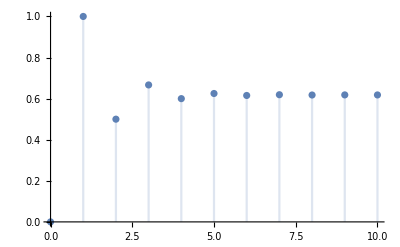

```mathematica
DiscretePlot[-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n),{n,0,10}]
```

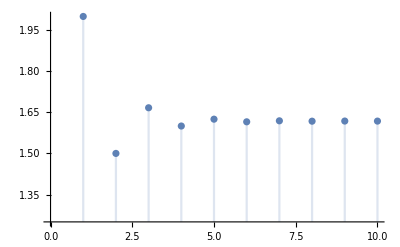

```mathematica
DiscretePlot[1-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n),{n,0,10}]
```

```mathematica
D[-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n),n]
```

-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n) Log[2])/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n)+(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n) (-((1-√5)/(1+√5))^n (ⅈ π+Log[-(1-√5)/(1+√5)])+√5 ((1-√5)/(1+√5))^n (ⅈ π+Log[-(1-√5)/(1+√5)])))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n)^2-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n (ⅈ π+Log[1/2 (-1+√5)])-(1/2 (1+√5))^n Log[1/2 (1+√5)]))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n)+(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n) Log[1+√5])/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n)

```mathematica
FourierSequenceTransform[%16,n,ω]
```

$Aborted